```mathematica
FunctE[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
FunctE1[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]

```mathematica
FunctE2[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
GammaSMLO[omega_,gammarx_,omegarx_]=gammarx*omega/omegarx
```

(gammarx omega)/omegarx

```mathematica
MainDirecroty=NotebookDirectory[]
```

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\

```mathematica
Filename="group_la_57_139.dat";
DataExp=ReadList[FileNameJoin[{MainDirecroty,Filename}],Number];
Ncolumbs=3;
Nmaxpoints1=Length[DataExp]/Ncolumbs-1;
X1aver=Table[DataExp[[Ncolumbs*i+1]],{i,0,Nmaxpoints1}];
Y1aver=Table[DataExp[[Ncolumbs*i+2]],{i,0,Nmaxpoints1}];
dY1aver=Table[DataExp[[Ncolumbs*i+3]],{i,0,Nmaxpoints1}];
Clear[DataExp]
```

```mathematica
Needs["ErrorBarPlots`"]
```

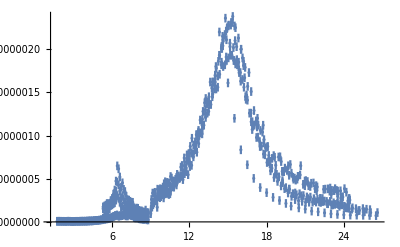

```mathematica
ErrorListPlot[{Transpose[{X1aver,Y1aver,dY1aver}]},PlotRange->All]
```

```mathematica
(* Fit  the cross section in the region [Ulow,Uupper] *)
```

```mathematica
Ulow=0.0;
Uupper=25.0;
Nlow=1;
Nupper=Length[Y1aver]
Do[If[X1aver[[i]]<Ulow,Nlow=i,Nlow=Nlow],{i,1,Length[Y1aver]}];
Do[If[X1aver[[i]]<Uupper,Nupper=i,Nupper=Nupper],{i,1,Length[Y1aver]}];
Nlow
Nupper
```

621

1

617

```mathematica
1
```

1

```mathematica
(*X1aver*)
```

```mathematica
(*Y1aver*)
```

```mathematica
(*dY1aver*)
```

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(0.000142804+((0.+«23» ⅈ) omega)/(41.1108+«1»«1»«1»))/(232.221+«1»-«1»+(8.42681×10^-14 «1»)/(41.1108+«1»-(«5»)^2))+(«1»)/(«1»)]]

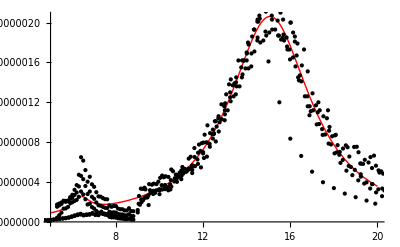

15.2388

6.41177

4.57267

1.

2.9029×10^-7

0.0119501

0.000955812

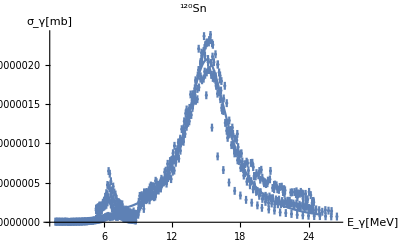

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1945.66] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1194.77] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.2388 | 0.0255785 | 595.765 | 0.
omega2p | 6.41177 | 0.192885 | 33.2414 | 4.78527×10^-139
Gamma1p | 4.57267 | 0.403351 | 11.3367 | 3.63488×10^-27
Gamma2p | 1. | 0.565199 | 1.76929 | 0.0773452
Gamma12p | 2.9029×10^-7 | 0.376304 | 7.71423×10^-7 | 0.999999
Z10 | 0.0119501 | 0.0000693318 | 172.361 | 0.
Z20 | 0.000955812 | 0.00012954 | 7.37849 | 5.25909×10^-13

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1945.66] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1194.77] is too small to represent as a normalized machine number; precision may be lost.

{{15.2388,0.0255785,595.765,0.},{6.41177,0.192885,33.2414,4.78527×10^-139},{4.57267,0.403351,11.3367,3.63488×10^-27},{1.,0.565199,1.76929,0.0773452},{2.9029×10^-7,0.376304,7.71423×10^-7,0.999999},{0.0119501,0.0000693318,172.361,0.},{0.000955812,0.00012954,7.37849,5.25909×10^-13}}

7.65062

7.65062

```mathematica
(*TSE  !!!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,Nlow,Nmaxpointstemp}];
FordY1aver=Table[dY1aver[[i]],{i,Nlow,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p < 20, 4<omega2p<8, 3<Gamma1p<8, 1<Gamma2p<3, 0<Gamma12p<6 (*, Z10<10, Z20<10*)
},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","120"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.000135504/(230.137+(0.+4.37589 ⅈ) omega-omega^2)+0.0000220155/(517.159+(0.+«1») «5»-omega^2)]]

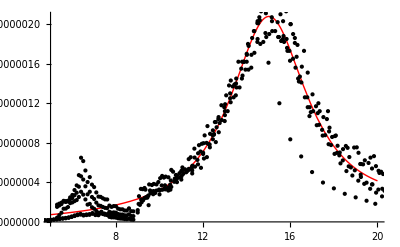

15.1703

22.7411

4.37589

7.75305

0.0116406

0.00469207

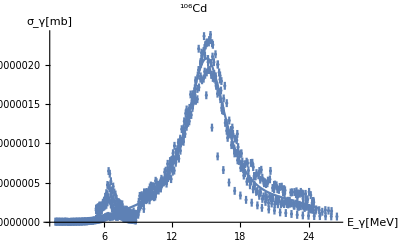

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1853.34] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.1703 | 0.0297562 | 509.818 | 0.
omega2p | 22.7411 | 0.810119 | 28.0714 | 5.26062×10^-112
Gamma1p | 4.37589 | 0.0953275 | 45.9038 | 3.37674×10^-200
Gamma2p | 7.75305 | 3.87875 | 1.99885 | 0.0460669
Z10 | 0.0116406 | 0.000156727 | 74.273 | 4.49183×10^-308
Z20 | 0.00469207 | 0.0010916 | 4.29834 | 0.0000200232

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1853.34] is too small to represent as a normalized machine number; precision may be lost.

{{15.1703,0.0297562,509.818,0.},{22.7411,0.810119,28.0714,5.26062×10^-112},{4.37589,0.0953275,45.9038,3.37674×10^-200},{7.75305,3.87875,1.99885,0.0460669},{0.0116406,0.000156727,74.273,4.49183×10^-308},{0.00469207,0.0010916,4.29834,0.0000200232}}

7.3703

7.3703

```mathematica
(*independent Gamma12p=0 !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0, 10<omega1p < 20 },{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam0[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam0=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(0.000918631+((0.+«21» ⅈ) omega)/(«1»))/(1447.51-(«5»)^2+«1»+(709.714 («5»)^2)/(123.777+«1»-«1»))+(«23»+(«1»)/(«1»))/(«19»+«1»«1»«1»+(«1»)/(«1»))]]

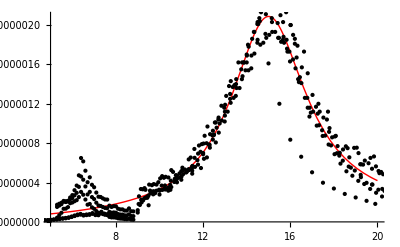

11.1255

38.0462

-13.6779

179.676

26.6405

0.00576551

0.0303089

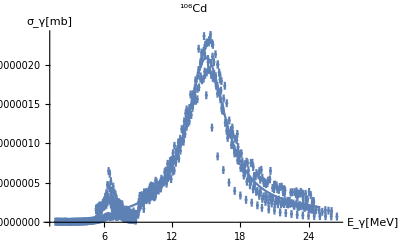

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 11.1255 | 5.38944 | 2.06432 | 0.0394099
omega2p | 38.0462 | 3.8365 | 9.91689 | 1.36305×10^-21
Gamma1p | -13.6779 | 4.24039 | -3.22563 | 0.00132419
Gamma2p | 179.676 | 54.3968 | 3.30306 | 0.00101231
Gamma12p | 26.6405 | 22.4338 | 1.18751 | 0.235487
Z10 | 0.00576551 | 0.00449842 | 1.28168 | 0.200443
Z20 | 0.0303089 | 0.00527843 | 5.74203 | 1.47609×10^-8

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{11.1255,5.38944,2.06432,0.0394099},{38.0462,3.8365,9.91689,1.36305×10^-21},{-13.6779,4.24039,-3.22563,0.00132419},{179.676,54.3968,3.30306,0.00101231},{26.6405,22.4338,1.18751,0.235487},{0.00576551,0.00449842,1.28168,0.200443},{0.0303089,0.00527843,5.74203,1.47609×10^-8}}

7.43223

7.43223

```mathematica
(*TSE SMLO GDR and PDR *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(0.000129702+((0.+«18» ⅈ) omega)/(«1»))/(227.878+ⅈ («17»-«21» omega) omega-«1»+(21.7583 («5»)^2)/(«1»))+(«21»+(«1»)/(«1»))/(«22»+«1»-«1»+(«1»)/(«1»))]]

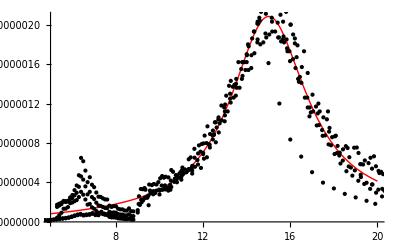

15.0956

35503.

-0.403264

360.127

4.66458

0.0113887

4302.23

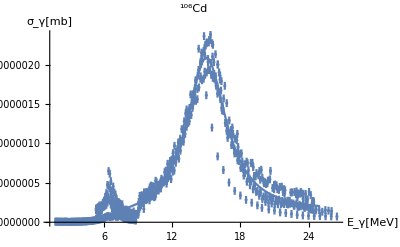

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.0956 | 0.509037 | 29.6553 | 2.38213×10^-120
omega2p | 35503. | 4465.36 | 7.95076 | 9.01473×10^-15
Gamma1p | -0.403264 | 6.5426 | -0.0616366 | 0.950872
Gamma2p | 360.127 | 3494.56 | 0.103054 | 0.917954
Gamma12p | 4.66458 | 6.35195 | 0.734354 | 0.463015
Z10 | 0.0113887 | 0.00024435 | 46.608 | 3.50475×10^-203
Z20 | 4302.23 | 18424.6 | 0.233504 | 0.815448

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{15.0956,0.509037,29.6553,2.38213×10^-120},{35503.,4465.36,7.95076,9.01473×10^-15},{-0.403264,6.5426,-0.0616366,0.950872},{360.127,3494.56,0.103054,0.917954},{4.66458,6.35195,0.734354,0.463015},{0.0113887,0.00024435,46.608,3.50475×10^-203},{4302.23,18424.6,0.233504,0.815448}}

7.42549

7.42549

```mathematica
(*TSE SMLO GDR and PDG G=const !!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[(0.000151097+((0.+«22» ⅈ) omega)/(«1»))/(245.189+«1»-«1»+(144.71 («5»)^2)/(227.321+«1»-«1»))+(«23»+(«1»)/(«1»))/(«19»+«1»«1»«1»+(«1»)/(«1»))]]

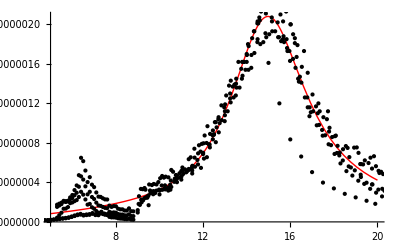

15.0772

15.6585

0.237851

11.076

12.0296

0.00561454

0.0122922

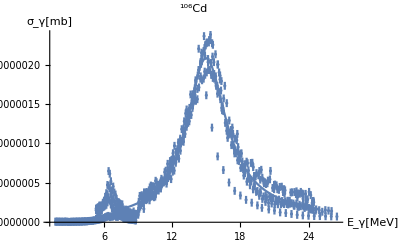

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.0772 | 0.749786 | 20.1087 | 2.21321×10^-69
omega2p | 15.6585 | 0.49578 | 31.5836 | 1.81895×10^-130
Gamma1p | 0.237851 | 15.5847 | 0.0152619 | 0.987828
Gamma2p | 11.076 | 35.3453 | 0.313365 | 0.75411
Gamma12p | 12.0296 | 11.3025 | 1.06433 | 0.2876
Z10 | 0.00561454 | 0.00640665 | 0.876361 | 0.381179
Z20 | 0.0122922 | 0.000500784 | 24.5459 | 4.60232×10^-93

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{15.0772,0.749786,20.1087,2.21321×10^-69},{15.6585,0.49578,31.5836,1.81895×10^-130},{0.237851,15.5847,0.0152619,0.987828},{11.076,35.3453,0.313365,0.75411},{12.0296,11.3025,1.06433,0.2876},{0.00561454,0.00640665,0.876361,0.381179},{0.0122922,0.000500784,24.5459,4.60232×10^-93}}

7.50025

7.50025

```mathematica
(*TSE SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(1.53923×10^-6)/(41.5497-(1.-0.148006 ⅈ) omega^2)+0.0001502/(233.701-(1.-«20» ⅈ) «1»)]]

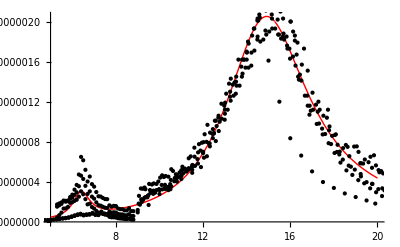

15.2873

6.4459

4.91522

0.954032

0.0122556

0.00124066

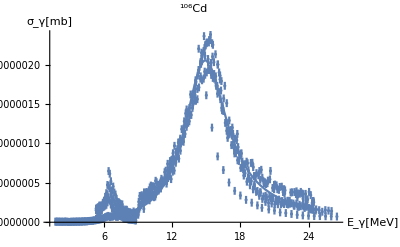

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1976.87] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-893.35] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1187.67] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.2873 | 0.0244873 | 624.293 | 0.
omega2p | 6.4459 | 0.0624918 | 103.148 | 0.
Gamma1p | 4.91522 | 0.0766373 | 64.1362 | 1.44528×10^-273
Gamma2p | 0.954032 | 0.187064 | 5.10002 | 4.53743×10^-7
Z10 | 0.0122556 | 0.0000721285 | 169.913 | 0.
Z20 | 0.00124066 | 0.0000867004 | 14.3097 | 2.87671×10^-40

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1976.87] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-893.35] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1187.67] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{15.2873,0.0244873,624.293,0.},{6.4459,0.0624918,103.148,0.},{4.91522,0.0766373,64.1362,1.44528×10^-273},{0.954032,0.187064,5.10002,4.53743×10^-7},{0.0122556,0.0000721285,169.913,0.},{0.00124066,0.0000867004,14.3097,2.87671×10^-40}}

7.08126

7.08126

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(1.52111×10^-6)/(41.5177+(0.+0.935895 ⅈ) omega-omega^2)+0.000150457/(233.702-(1.-«1») «1»)]]

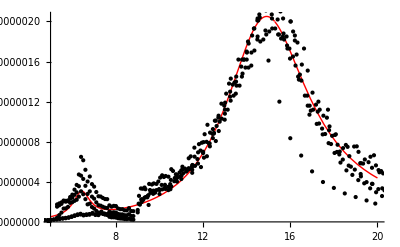

15.2873

6.44342

4.92368

0.935895

0.0122661

0.00123333

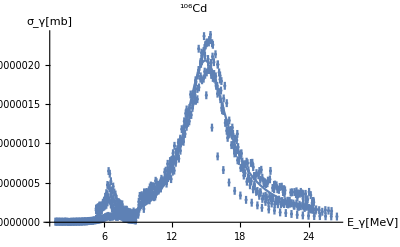

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1976.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-906.119] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1191.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.2873 | 0.0245134 | 623.631 | 0.
omega2p | 6.44342 | 0.0611041 | 105.45 | 0.
Gamma1p | 4.92368 | 0.0764578 | 64.3973 | 1.66184×10^-274
Gamma2p | 0.935895 | 0.17984 | 5.20404 | 2.66638×10^-7
Z10 | 0.0122661 | 0.0000717653 | 170.919 | 0.
Z20 | 0.00123333 | 0.0000844873 | 14.5979 | 1.27215×10^-41

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1976.23] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-906.119] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1191.2] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{15.2873,0.0245134,623.631,0.},{6.44342,0.0611041,105.45,0.},{4.92368,0.0764578,64.3973,1.66184×10^-274},{0.935895,0.17984,5.20404,2.66638×10^-7},{0.0122661,0.0000717653,170.919,0.},{0.00123333,0.0000844873,14.5979,1.27215×10^-41}}

7.08064

7.08064

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG G=const !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[-Im[0.000144639/(232.265+(0.+4.6524 ⅈ) omega-omega^2)+4672.45/(1.06475×10^-14-(1.+«1») «1»)]]

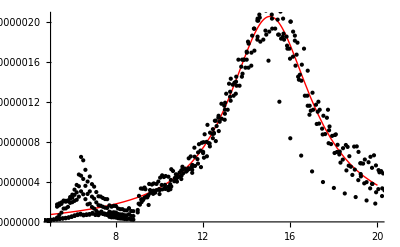

15.2402

-1.03187×10^-7

4.6524

5566.47

0.0120266

68.3553

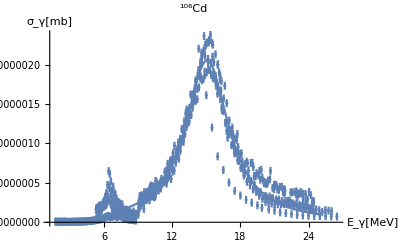

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1985.74] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-22210.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1222.15] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 15.2402 | 0.0240599 | 633.43 | 0.
omega2p | -1.03187×10^-7 | 1.63133×10^-7 | -0.632531 | 0.527277
Gamma1p | 4.6524 | 0.0677149 | 68.7058 | 1.31421×10^-289
Gamma2p | 5566.47 | 3.6999×10^-14 | 1.50449×10^17 | 0.
Z10 | 0.0120266 | 0.0000668221 | 179.979 | 0.
Z20 | 68.3553 | 1.29937×10^-12 | 5.26066×10^13 | 0.

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-1985.74] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-22210.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1222.15] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{15.2402,0.0240599,633.43,0.},{-1.03187×10^-7,1.63133×10^-7,-0.632531,0.527277},{4.6524,0.0677149,68.7058,1.31421×10^-289},{5566.47,3.6999×10^-14,1.50449×10^17,0.},{0.0120266,0.0000668221,179.979,0.},{68.3553,1.29937×10^-12,5.26066×10^13,0.}}

8.07699

8.07699

```mathematica
(*independent Gamma12p=0, SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

```mathematica
"E:\\Sasha\\work\\Students\\Kucher\\Cd106\\FigSigmaFit106Cd.eps"
```

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

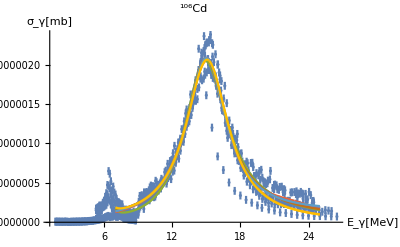

```mathematica
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[{ResponseFuncPDRsmloGDRsmlo[x],ResponseFuncPDRsmloGDRcons[x],ResponseFuncPDRconsGDRsmlo[x],ResponseFuncTSEgam0[x],ResponseFuncTSEPDRsmloGDRsmlo[x],ResponseFuncTSEPDRsmloGDRcons[x],ResponseFuncTSEPDRconsGDRsmlo[x],ResponseFuncTSEgam[x]},{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
```

```mathematica
Chi2PDRsmloGDRsmlo
Chi2PDRsmloGDRcons
Chi2PDRconsGDRsmlo
Chi2TSEgam0
Chi2TSEPDRsmloGDRsmlo
Chi2TSEPDRsmloGDRcons
Chi2TSEPDRconsGDRsmlo
Chi2TSEgam
```

7.08126

8.07699

7.08064

7.3703

7.43223

7.50025

7.42549

7.65062